## MOIs evolution across all four fitting approaches

## Step for the MOI: 1

```mathematica
i1values={76,73,78,73};
i2values={52,3,5,68};
i3values={3,67,14,3};
```

```mathematica
vPlot[values_]:=ListPlot[values,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,PlotRange->{{0.8,4.2},{1,6}},FrameStyle->Directive[Thick,Black],FrameLabel->{"","V [MeV]"},LabelStyle->{20,Black,Bold,FontFamily->"Times New Roman"},FrameTicks->{Automatic,{{{1,"A1"},{2,"A2"},{3,"B1"},{4,"B2"}},None}},Epilog->{Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.5,0.25}]],Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.9,0.75}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.68,0.75}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.10,0.25}]]},ImageSize->Large];
```

```mathematica
plotMOIs[mois1_,mois2_,mois3_]:=ListPlot[{mois1,mois2,mois3},Joined->True,Joined->True,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},PlotMarkers->{Automatic, 12},AspectRatio->0.75,Frame->True,Axes->False,PlotRange->{{0.8,4.2},Automatic},FrameStyle->Directive[Thick,Black],FrameLabel->{"","ℐ [ℏ^2/MeV]"},LabelStyle->{20,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Large,FrameTicks->{Automatic,{{{1,"A1"},{2,"A2"},{3,"B1"},{4,"B2"}},None}},PlotLegends->{"ℐ_1","ℐ_2","ℐ_3"}];
```

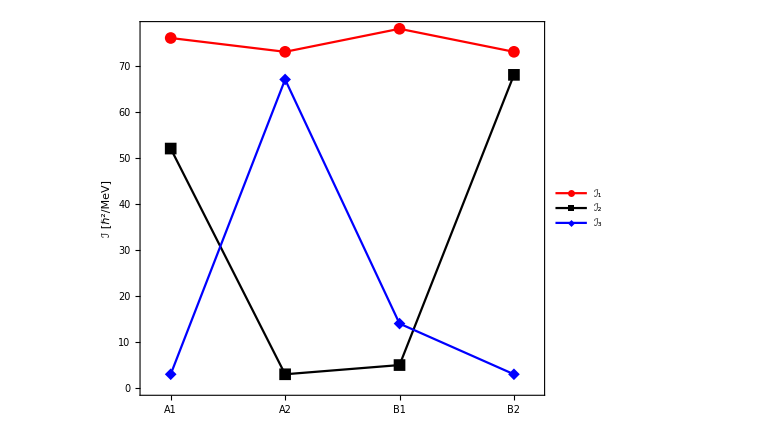

```mathematica
Show[plotMOIs[i1values,i2values,i3values]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/MOI_evolution.png",Show[plotMOIs[i1values,i2values,i3values]]];
```

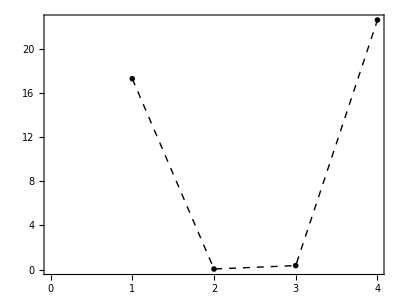

```mathematica
moiRatio23=Table[i2values[[i]]/i3values[[i]],{i,1,Length[i1values]}];
ListPlot[moiRatio23,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black]]
```

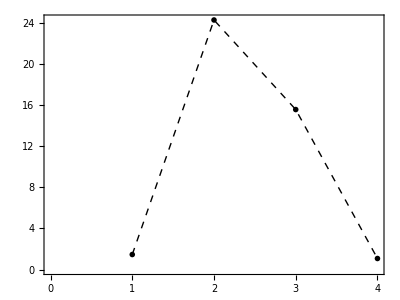

```mathematica
moiRatio12=Table[i1values[[i]]/i2values[[i]],{i,1,Length[i1values]}];
ListPlot[moiRatio12,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black]]
```

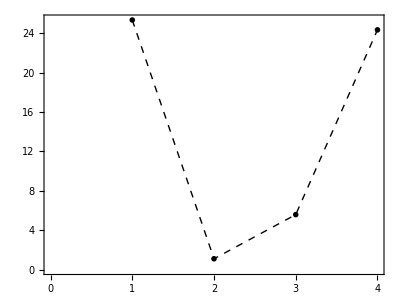

```mathematica
moiRatio13=Table[i1values[[i]]/i3values[[i]],{i,1,Length[i1values]}];
ListPlot[moiRatio13,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black]]
```